```mathematica
ImagePartition[GeoGraphics[Here, GeoRange->Quantity[0.5,"Miles"]], 150]//Grid
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
GeoEntities[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],Quantity[2,"Kilometers"]],"Building"]
```

{770 Eastern Parkway,Church of Our Lady of Victory,Church of Saint Francis of Assisi and Saint Blaise,St. Blaise's Church}

```mathematica
analyzeCityTiles[cityEntity_,tileSize_,entityType_]:=Module[{center,region,bounds,latRange,lonRange,latStep,lonStep,latitudes,longitudes,tileBoxes,tileFeatures},(*Get the city's geographic center*)center=EntityValue[cityEntity,"Position"];
(*Define analysis region around center (1 km radius)*)region=GeoDisk[center,Quantity[1,"Kilometers"]];
bounds=GeoBounds[region];
(*Approximate tile step sizes in degrees*)latStep=QuantityMagnitude@GeoDistance[GeoPosition[{bounds[[1,1]],bounds[[1,2]]}],GeoPosition[{bounds[[1,1]]+0.005,bounds[[1,2]]}]];
lonStep=QuantityMagnitude@GeoDistance[GeoPosition[{bounds[[1,1]],bounds[[1,2]]}],GeoPosition[{bounds[[1,1]],bounds[[1,2]]+0.005}]];
(*Create latitude and longitude grid*)latitudes=Range[bounds[[1,1]],bounds[[2,1]],tileSize/111320.];(*1 deg≈111.32 km*)longitudes=Range[bounds[[1,2]],bounds[[2,2]],tileSize/111320.];
(*Build tiles centered at lat/lon grid points*)tileBoxes=Flatten[Table[GeoBoundingBox[GeoPosition[{lat,lon}],Quantity[tileSize/2,"Meters"]],{lat,latitudes},{lon,longitudes}],1];
(*Count and extract entities in each tile*)tileFeatures=Table[With[{entities=Quiet@GeoEntities[tileBoxes[[i]],entityType]},<|"TileIndex"->i,"BoundingBox"->tileBoxes[[i]],"EntityCount"->Length[entities],"EntityPositions"->Quiet@EntityValue[entities,"Position"]|>],{i,Length[tileBoxes]}];
Dataset[tileFeatures]]

boston=Entity["City",{"Boston","Massachusetts","UnitedStates"}];
analyzeCityTiles[boston,500,"Building"]
```

```mathematica
cityEntity = Entity["City",{"Boston","Massachusetts","UnitedStates"}]; (*Boston*) 
tileSize = 500;
entityType = "Building";
center=EntityValue[cityEntity,"Position"];
region=GeoDisk[center,Quantity[1,"Kilometers"]];
bounds=GeoBounds[region];
```

500

Building

```mathematica
osm=OSMImport[GeoBoundsRegion[{{40.0923,40.0991},{-48.2586,-48.2479}}]];
```

```mathematica
(*Step 1:Load the region*)openStreetMapRegion=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]];



(*(*Step 2:Filter for roads only*)
roadWays=Select[openStreetMapRegion["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&];

(*Step 3:Build Line graphics primitives from node coordinates*)
roadLines=Line[openStreetMapRegion[["Nodes",#Nodes,"Position"]]]&/@roadWays;*)
```

```mathematica
Line[Values[openStreetMapRegion[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapRegion["Ways"],MatchQ[#[["Tags","highway"]],"residential"]&]
```

<|5669664→Line[{GeoPosition[{40.7639,-73.9741}],GeoPosition[{40.7637,-73.9736}],GeoPosition[{40.7637,-73.9735}]}],5670029→Line[{GeoPosition[{40.7674,-73.9707}],GeoPosition[{40.7674,-73.9706}],GeoPosition[{40.7668,-73.9693}],GeoPosition[{40.7668,-73.9692}],GeoPosition[{40.7667,-73.9691}],GeoPosition[{40.7667,-73.969}],GeoPosition[{40.7667,-73.969}],GeoPosition[{40.7662,-73.9678}],GeoPosition[{40.7661,-73.9677}],GeoPosition[{40.7661,-73.9676}],GeoPosition[{40.766,-73.9674}],GeoPosition[{40.766,-73.9673}],GeoPosition[{40.7654,-73.966}],GeoPosition[{40.7654,-73.9659}],GeoPosition[{40.7653,-73.9658}],GeoPosition[{40.7647,-73.9644}],GeoPosition[{40.7647,-73.9643}],GeoPosition[{40.7646,-73.9642}],GeoPosition[{40.7638,-73.9622}],GeoPosition[{40.7637,-73.9621}],GeoPosition[{40.7637,-73.962}],GeoPosition[{40.7637,-73.9619}],GeoPosition[{40.7628,-73.9598}],GeoPosition[{40.7627,-73.9597}]}],5670034→Line[{GeoPosition[{40.7699,-73.9689}],GeoPosition[{40.7699,-73.9688}],GeoPosition[{40.7693,-73.9674}],GeoPosition[{40.7692,-73.9673}]}],5670197→Line[{GeoPosition[{40.7559,-73.9945}],GeoPosition[{40.7559,-73.9943}],GeoPosition[{40.7549,-73.9921}]}],5671115→Line[{GeoPosition[{40.7646,-73.9955}],GeoPosition[{40.7646,-73.9954}],GeoPosition[{40.7644,-73.995}],GeoPosition[{40.7638,-73.9935}],GeoPosition[{40.7635,-73.9928}],GeoPosition[{40.7634,-73.9927}],GeoPosition[{40.7634,-73.9926}],GeoPosition[{40.7623,-73.99}],GeoPosition[{40.7622,-73.9899}],GeoPosition[{40.7622,-73.9897}],GeoPosition[{40.7614,-73.9879}],GeoPosition[{40.7611,-73.9872}],GeoPosition[{40.7611,-73.9871}]}],5671129→Line[{GeoPosition[{40.7623,-73.9745}],GeoPosition[{40.7622,-73.9743}],GeoPosition[{40.7617,-73.973}],GeoPosition[{40.7616,-73.9729}]}],5671629→Line[{GeoPosition[{40.7573,-73.9781}],GeoPosition[{40.7572,-73.978}],GeoPosition[{40.7566,-73.9766}],GeoPosition[{40.7566,-73.9765}]}],5672036→Line[{GeoPosition[{40.7567,-73.9786}],GeoPosition[{40.7567,-73.9787}],GeoPosition[{40.7567,-73.9787}],GeoPosition[{40.758,-73.9817}],GeoPosition[{40.758,-73.9818}],GeoPosition[{40.7581,-73.9819}],GeoPosition[{40.7583,-73.9825}],GeoPosition[{40.7592,-73.9845}],GeoPosition[{40.7592,-73.9846}]}],5672118→Line[{GeoPosition[{40.7591,-73.9747}],GeoPosition[{40.7591,-73.9746}],GeoPosition[{40.7586,-73.9733}],GeoPosition[{40.7585,-73.9733}],GeoPosition[{40.7585,-73.9732}]}],5672951→Line[{GeoPosition[{40.763,-73.9719}],GeoPosition[{40.7629,-73.9718}],GeoPosition[{40.7625,-73.9708}]}],5673461→Line[{GeoPosition[{40.7661,-73.9717}],GeoPosition[{40.7661,-73.9715}],GeoPosition[{40.7655,-73.9702}],GeoPosition[{40.7655,-73.9702}],GeoPosition[{40.7655,-73.97}],GeoPosition[{40.7654,-73.9699}],GeoPosition[{40.7649,-73.9687}],GeoPosition[{40.7649,-73.9686}],GeoPosition[{40.7648,-73.9685}],GeoPosition[{40.7648,-73.9683}],GeoPosition[{40.7647,-73.9682}],GeoPosition[{40.7642,-73.9669}],GeoPosition[{40.7641,-73.9668}],GeoPosition[{40.7641,-73.9667}],GeoPosition[{40.7635,-73.9654}],GeoPosition[{40.7634,-73.9652}]}],46482604→Line[{GeoPosition[{40.7631,-73.9938}],GeoPosition[{40.7632,-73.994}]}],46482609→Line[{GeoPosition[{40.7609,-73.9945}],GeoPosition[{40.7609,-73.9944}],GeoPosition[{40.7598,-73.9918}],GeoPosition[{40.7597,-73.9917}]}],46522160→Line[{GeoPosition[{40.7631,-73.9625}],GeoPosition[{40.7632,-73.9627}],GeoPosition[{40.764,-73.9646}],GeoPosition[{40.7641,-73.9648}],GeoPosition[{40.7641,-73.9649}],GeoPosition[{40.7647,-73.9663}],GeoPosition[{40.7647,-73.9664}],GeoPosition[{40.7648,-73.9665}],GeoPosition[{40.7653,-73.9677}],GeoPosition[{40.7653,-73.9678}],GeoPosition[{40.7654,-73.9679}],GeoPosition[{40.7655,-73.9681}],GeoPosition[{40.7655,-73.9682}],GeoPosition[{40.766,-73.9695}],GeoPosition[{40.7661,-73.9696}],GeoPosition[{40.7661,-73.9697}],GeoPosition[{40.7661,-73.9697}],GeoPosition[{40.7667,-73.9711}],GeoPosition[{40.7668,-73.9712}]}],46538335→Line[{GeoPosition[{40.7592,-73.9767}],GeoPosition[{40.7592,-73.9769}],GeoPosition[{40.7596,-73.9778}],GeoPosition[{40.7597,-73.978}],GeoPosition[{40.7597,-73.9781}],GeoPosition[{40.7603,-73.9795}]}],167922073→Line[{GeoPosition[{40.7598,-73.9842}],GeoPosition[{40.7598,-73.9841}],GeoPosition[{40.7594,-73.9832}],GeoPosition[{40.7593,-73.983}],GeoPosition[{40.759,-73.9821}]}],167922074→Line[{GeoPosition[{40.7601,-73.9848}],GeoPosition[{40.7601,-73.9848}],GeoPosition[{40.7601,-73.9847}],GeoPosition[{40.7599,-73.9843}],GeoPosition[{40.7598,-73.9842}]}],194926847→Line[{GeoPosition[{40.7591,-73.9921}],GeoPosition[{40.7592,-73.9923}],GeoPosition[{40.76,-73.9943}]}],198595461→Line[{GeoPosition[{40.7619,-73.9634}],GeoPosition[{40.7619,-73.9636}],GeoPosition[{40.7627,-73.9654}],GeoPosition[{40.7628,-73.9655}],GeoPosition[{40.7628,-73.9657}],GeoPosition[{40.7629,-73.9658}],GeoPosition[{40.7634,-73.9672}],GeoPosition[{40.7635,-73.9673}],GeoPosition[{40.7635,-73.9674}],GeoPosition[{40.7641,-73.9686}],GeoPosition[{40.7641,-73.9687}],GeoPosition[{40.7641,-73.9688}],GeoPosition[{40.7642,-73.969}],GeoPosition[{40.7643,-73.9691}],GeoPosition[{40.7647,-73.9702}]}],226041007→Line[{GeoPosition[{40.756,-73.975}],GeoPosition[{40.7559,-73.9748}]}],226041013→Line[{GeoPosition[{40.7596,-73.9701}],GeoPosition[{40.7597,-73.9702}],GeoPosition[{40.7598,-73.9705}],GeoPosition[{40.7602,-73.9714}],GeoPosition[{40.7602,-73.9715}],GeoPosition[{40.7603,-73.9716}],GeoPosition[{40.7604,-73.9718}]}],226041021→Line[{GeoPosition[{40.7565,-73.994}],GeoPosition[{40.7566,-73.9942}],GeoPosition[{40.7568,-73.9947}],GeoPosition[{40.7569,-73.9948}],GeoPosition[{40.757,-73.9951}]}],226041023→Line[{GeoPosition[{40.7572,-73.9936}],GeoPosition[{40.7571,-73.9935}]}],226041025→Line[{GeoPosition[{40.7555,-73.9836}],GeoPosition[{40.7556,-73.9838}],GeoPosition[{40.7561,-73.9851}],GeoPosition[{40.7563,-73.9854}],GeoPosition[{40.7564,-73.9858}]}],226041026→Line[{GeoPosition[{40.7572,-73.9857}],GeoPosition[{40.7565,-73.984}],GeoPosition[{40.7562,-73.9833}],GeoPosition[{40.7561,-73.9832}]}],226041027→Line[{GeoPosition[{40.7597,-73.9917}],GeoPosition[{40.7597,-73.9916}],GeoPosition[{40.7588,-73.9895}],GeoPosition[{40.7586,-73.989}],GeoPosition[{40.7585,-73.9888}]}],226041028→Line[{GeoPosition[{40.761,-73.987}],GeoPosition[{40.761,-73.9869}],GeoPosition[{40.7605,-73.9857}],GeoPosition[{40.7604,-73.9854}],GeoPosition[{40.7602,-73.9849}],GeoPosition[{40.7601,-73.9848}]}],226041029→Line[{GeoPosition[{40.7586,-73.9813}],GeoPosition[{40.7586,-73.9812}],GeoPosition[{40.7579,-73.9795}],GeoPosition[{40.7578,-73.9794}],GeoPosition[{40.7578,-73.9793}],GeoPosition[{40.7573,-73.9782}],GeoPosition[{40.7573,-73.9781}]}],226041030→Line[{GeoPosition[{40.7621,-73.9837}],GeoPosition[{40.7621,-73.9837}],GeoPosition[{40.7621,-73.9838}],GeoPosition[{40.7626,-73.9848}],GeoPosition[{40.7629,-73.9855}],GeoPosition[{40.7629,-73.9856}]}],226041031→Line[{GeoPosition[{40.7629,-73.9856}],GeoPosition[{40.763,-73.9858}]}],308322446→Line[{GeoPosition[{40.7674,-73.9824}],GeoPosition[{40.7673,-73.9822}],GeoPosition[{40.7672,-73.9818}],GeoPosition[{40.7671,-73.9817}]}],308322447→Line[{GeoPosition[{40.7662,-73.9795}],GeoPosition[{40.7662,-73.9794}],GeoPosition[{40.7651,-73.9768}],GeoPosition[{40.765,-73.9767}],GeoPosition[{40.7649,-73.9766}],GeoPosition[{40.764,-73.9742}],GeoPosition[{40.7639,-73.9741}]}],425335557→Line[{GeoPosition[{40.7689,-73.982}],GeoPosition[{40.7689,-73.9821}],GeoPosition[{40.7689,-73.9821}],GeoPosition[{40.769,-73.9822}]}],439768850→Line[{GeoPosition[{40.7566,-73.9765}],GeoPosition[{40.7566,-73.9764}],GeoPosition[{40.756,-73.9751}],GeoPosition[{40.756,-73.9751}],GeoPosition[{40.756,-73.975}]}],452322756→Line[{GeoPosition[{40.7594,-73.9851}],GeoPosition[{40.7595,-73.9852}],GeoPosition[{40.7595,-73.9853}],GeoPosition[{40.7602,-73.9871}],GeoPosition[{40.7604,-73.9873}],GeoPosition[{40.7604,-73.9875}],GeoPosition[{40.7605,-73.9876}],GeoPosition[{40.7605,-73.9876}],GeoPosition[{40.7615,-73.9902}],GeoPosition[{40.7616,-73.9903}]}],452322757→Line[{GeoPosition[{40.7592,-73.9846}],GeoPosition[{40.7593,-73.9847}],GeoPosition[{40.7594,-73.985}],GeoPosition[{40.7594,-73.9851}]}],464515890→Line[{GeoPosition[{40.7561,-73.9832}],GeoPosition[{40.7561,-73.983}],GeoPosition[{40.755,-73.9805}]}],496992867→Line[{GeoPosition[{40.7598,-73.9763}],GeoPosition[{40.7598,-73.9762}],GeoPosition[{40.7592,-73.9748}],GeoPosition[{40.7591,-73.9747}]}],499172074→Line[{GeoPosition[{40.763,-73.9781}],GeoPosition[{40.7631,-73.9783}],GeoPosition[{40.7635,-73.9792}],GeoPosition[{40.7635,-73.9793}],GeoPosition[{40.7635,-73.9793}],GeoPosition[{40.7636,-73.9794}],GeoPosition[{40.7638,-73.9798}],GeoPosition[{40.7638,-73.9799}],GeoPosition[{40.7642,-73.9809}],GeoPosition[{40.7642,-73.981}],GeoPosition[{40.7643,-73.9811}],GeoPosition[{40.7646,-73.9819}],GeoPosition[{40.7647,-73.9821}],GeoPosition[{40.7648,-73.9823}],GeoPosition[{40.7648,-73.9823}],GeoPosition[{40.765,-73.9828}],GeoPosition[{40.7654,-73.9836}],GeoPosition[{40.7654,-73.9837}],GeoPosition[{40.7654,-73.9838}],GeoPosition[{40.7655,-73.9839}],GeoPosition[{40.7655,-73.9839}],GeoPosition[{40.7655,-73.984}],GeoPosition[{40.7656,-73.9843}],GeoPosition[{40.7666,-73.9865}],GeoPosition[{40.7666,-73.9866}],GeoPosition[{40.7666,-73.9867}],GeoPosition[{40.7667,-73.9868}],GeoPosition[{40.7678,-73.9893}],GeoPosition[{40.7678,-73.9894}],GeoPosition[{40.7678,-73.9895}],GeoPosition[{40.7679,-73.9896}],GeoPosition[{40.7689,-73.9921}],GeoPosition[{40.769,-73.9922}],GeoPosition[{40.769,-73.9923}]}],505317783→Line[{GeoPosition[{40.7553,-73.9912}],GeoPosition[{40.7554,-73.9913}],GeoPosition[{40.7557,-73.992}],GeoPosition[{40.7562,-73.9931}]}],505317789→Line[{GeoPosition[{40.7566,-73.9922}],GeoPosition[{40.756,-73.9909}],GeoPosition[{40.7559,-73.9907}]}],528748997→Line[{GeoPosition[{40.7616,-73.9729}],GeoPosition[{40.7616,-73.9727}],GeoPosition[{40.7614,-73.9723}],GeoPosition[{40.7613,-73.9722}],GeoPosition[{40.7612,-73.972}],GeoPosition[{40.7611,-73.9717}],GeoPosition[{40.761,-73.9715}],GeoPosition[{40.761,-73.9714}],GeoPosition[{40.761,-73.9713}],GeoPosition[{40.7609,-73.9712}],GeoPosition[{40.7609,-73.971}],GeoPosition[{40.7603,-73.9697}],GeoPosition[{40.7603,-73.9696}],GeoPosition[{40.7602,-73.9695}],GeoPosition[{40.7596,-73.9682}],GeoPosition[{40.7596,-73.9681}]}],542258060→Line[{GeoPosition[{40.7559,-73.9907}],GeoPosition[{40.7559,-73.9906}],GeoPosition[{40.7548,-73.988}],GeoPosition[{40.7548,-73.9879}]}],542371971→Line[{GeoPosition[{40.7698,-73.9822}],GeoPosition[{40.7697,-73.982}]}],544812894→Line[{GeoPosition[{40.7594,-73.9694}],GeoPosition[{40.7596,-73.97}],GeoPosition[{40.7596,-73.9701}]}],569345508→Line[{GeoPosition[{40.7575,-73.9729}],GeoPosition[{40.7577,-73.9733}],GeoPosition[{40.7577,-73.9733}],GeoPosition[{40.7578,-73.9734}]}],569345518→Line[{GeoPosition[{40.7579,-73.9736}],GeoPosition[{40.7579,-73.9737}],GeoPosition[{40.7583,-73.9747}]}],569345525→Line[{GeoPosition[{40.7583,-73.9747}],GeoPosition[{40.7584,-73.975}],GeoPosition[{40.7585,-73.9751}]}],569345531→Line[{GeoPosition[{40.7585,-73.9751}],GeoPosition[{40.7585,-73.9753}],GeoPosition[{40.7589,-73.9762}]}],569345535→Line[{GeoPosition[{40.7589,-73.9762}],GeoPosition[{40.7591,-73.9766}],GeoPosition[{40.7592,-73.9767}]}],569345536→Line[{GeoPosition[{40.7603,-73.9795}],GeoPosition[{40.7605,-73.9798}],GeoPosition[{40.7605,-73.98}]}],569345538→Line[{GeoPosition[{40.7605,-73.98}],GeoPosition[{40.7606,-73.9801}],GeoPosition[{40.7609,-73.9808}],GeoPosition[{40.7611,-73.9814}],GeoPosition[{40.7612,-73.9816}],GeoPosition[{40.7612,-73.9817}],GeoPosition[{40.7615,-73.9823}]}],569345539→Line[{GeoPosition[{40.7615,-73.9823}],GeoPosition[{40.7617,-73.9827}],GeoPosition[{40.7617,-73.9828}]}],569345541→Line[{GeoPosition[{40.7619,-73.9832}],GeoPosition[{40.762,-73.9835}],GeoPosition[{40.7621,-73.9837}]}],569345543→Line[{GeoPosition[{40.7567,-73.9865}],GeoPosition[{40.7568,-73.9866}],GeoPosition[{40.7575,-73.9884}]}],618990022→Line[{GeoPosition[{40.7696,-73.9919}],GeoPosition[{40.7696,-73.9918}],GeoPosition[{40.7693,-73.9911}],GeoPosition[{40.7688,-73.99}],GeoPosition[{40.7687,-73.9897}],GeoPosition[{40.7685,-73.9892}],GeoPosition[{40.7684,-73.989}],GeoPosition[{40.7684,-73.9889}],GeoPosition[{40.7673,-73.9863}],GeoPosition[{40.7672,-73.9862}],GeoPosition[{40.7672,-73.9861}],GeoPosition[{40.7666,-73.9848}],GeoPosition[{40.7666,-73.9846}],GeoPosition[{40.7664,-73.9843}],GeoPosition[{40.7661,-73.9835}],GeoPosition[{40.766,-73.9834}],GeoPosition[{40.766,-73.9832}],GeoPosition[{40.7655,-73.9821}],GeoPosition[{40.7655,-73.982}],GeoPosition[{40.7654,-73.9819}],GeoPosition[{40.7654,-73.9819}],GeoPosition[{40.7652,-73.9814}],GeoPosition[{40.7649,-73.9806}],GeoPosition[{40.7648,-73.9805}],GeoPosition[{40.7648,-73.9804}],GeoPosition[{40.7645,-73.9797}],GeoPosition[{40.7645,-73.9796}],GeoPosition[{40.7644,-73.9795}],GeoPosition[{40.7644,-73.9794}],GeoPosition[{40.7643,-73.9793}],GeoPosition[{40.7642,-73.9789}],GeoPosition[{40.7641,-73.9789}],GeoPosition[{40.7639,-73.9783}],GeoPosition[{40.7637,-73.9778}],GeoPosition[{40.7636,-73.9777}],GeoPosition[{40.7636,-73.9776}],GeoPosition[{40.7635,-73.9772}],GeoPosition[{40.7633,-73.9769}],GeoPosition[{40.7631,-73.9764}],GeoPosition[{40.7623,-73.9746}],GeoPosition[{40.7623,-73.9745}]}],658583340→Line[{GeoPosition[{40.7555,-73.9681}],GeoPosition[{40.7556,-73.9682}],GeoPosition[{40.7564,-73.9702}],GeoPosition[{40.7565,-73.9703}],GeoPosition[{40.7565,-73.9704}],GeoPosition[{40.7568,-73.971}],GeoPosition[{40.7568,-73.9712}],GeoPosition[{40.7571,-73.9718}],GeoPosition[{40.7571,-73.9719}]}],663612299→Line[{GeoPosition[{40.763,-73.9858}],GeoPosition[{40.763,-73.9858}],GeoPosition[{40.7636,-73.9872}],GeoPosition[{40.7637,-73.9875}],GeoPosition[{40.7641,-73.9884}],GeoPosition[{40.7641,-73.9885}]}],663612305→Line[{GeoPosition[{40.7611,-73.9871}],GeoPosition[{40.761,-73.987}]}],671208356→Line[{GeoPosition[{40.7623,-73.9702}],GeoPosition[{40.7622,-73.9701}],GeoPosition[{40.7618,-73.969}]}],710571387→Line[{GeoPosition[{40.759,-73.9685}],GeoPosition[{40.759,-73.9686}],GeoPosition[{40.7594,-73.9694}]}],717625447→Line[{GeoPosition[{40.7623,-73.9823}],GeoPosition[{40.7623,-73.9822}],GeoPosition[{40.7623,-73.9822}],GeoPosition[{40.7619,-73.9813}],GeoPosition[{40.7619,-73.9812}],GeoPosition[{40.7616,-73.9805}],GeoPosition[{40.7612,-73.9796}],GeoPosition[{40.7612,-73.9795}],GeoPosition[{40.7611,-73.9794}],GeoPosition[{40.7608,-73.9788}],GeoPosition[{40.7608,-73.9787}],GeoPosition[{40.7607,-73.9785}],GeoPosition[{40.7606,-73.9782}]}],717625448→Line[{GeoPosition[{40.7627,-73.9833}],GeoPosition[{40.7627,-73.9831}],GeoPosition[{40.7626,-73.9831}],GeoPosition[{40.7624,-73.9825}],GeoPosition[{40.7624,-73.9825}],GeoPosition[{40.7623,-73.9823}]}],743358442→Line[{GeoPosition[{40.7606,-73.9782}],GeoPosition[{40.7605,-73.978}],GeoPosition[{40.76,-73.9767}]}],743358443→Line[{GeoPosition[{40.7578,-73.9714}],GeoPosition[{40.7577,-73.9713}],GeoPosition[{40.7571,-73.97}],GeoPosition[{40.7571,-73.9699}],GeoPosition[{40.757,-73.9697}],GeoPosition[{40.7568,-73.9692}],GeoPosition[{40.7568,-73.9692}]}],743358444→Line[{GeoPosition[{40.7585,-73.9732}],GeoPosition[{40.7584,-73.973}],GeoPosition[{40.7584,-73.9729}],GeoPosition[{40.7581,-73.9722}],GeoPosition[{40.7578,-73.9716}],GeoPosition[{40.7578,-73.9714}]}],743358445→Line[{GeoPosition[{40.7568,-73.9692}],GeoPosition[{40.7562,-73.9677}],GeoPosition[{40.7561,-73.9676}],GeoPosition[{40.7561,-73.9675}],GeoPosition[{40.7552,-73.9654}],GeoPosition[{40.7552,-73.9654}],GeoPosition[{40.7551,-73.9652}]}],814278018→Line[{GeoPosition[{40.7653,-73.9913}],GeoPosition[{40.7654,-73.9915}],GeoPosition[{40.7656,-73.992}],GeoPosition[{40.7657,-73.9924}],GeoPosition[{40.7664,-73.9938}],GeoPosition[{40.7664,-73.9939}],GeoPosition[{40.7665,-73.994}],GeoPosition[{40.7665,-73.9942}]}],814278021→Line[{GeoPosition[{40.7641,-73.9885}],GeoPosition[{40.7642,-73.9886}],GeoPosition[{40.7653,-73.9912}],GeoPosition[{40.7653,-73.9913}]}],835176556→Line[{GeoPosition[{40.7697,-73.982}],GeoPosition[{40.7697,-73.9819}],GeoPosition[{40.7695,-73.9816}],GeoPosition[{40.7695,-73.9815}],GeoPosition[{40.7695,-73.9815}],GeoPosition[{40.7695,-73.9815}],GeoPosition[{40.7694,-73.9814}],GeoPosition[{40.7693,-73.9812}],GeoPosition[{40.7693,-73.9811}]}],847002232→Line[{GeoPosition[{40.7576,-73.9946}],GeoPosition[{40.7575,-73.9945}],GeoPosition[{40.7575,-73.9945}],GeoPosition[{40.7575,-73.9945}],GeoPosition[{40.7572,-73.9937}],GeoPosition[{40.7572,-73.9936}]}],965833822→Line[{GeoPosition[{40.7671,-73.9937}],GeoPosition[{40.7671,-73.9936}],GeoPosition[{40.7664,-73.9919}],GeoPosition[{40.7662,-73.9915}],GeoPosition[{40.766,-73.991}],GeoPosition[{40.7659,-73.9909}],GeoPosition[{40.7659,-73.9908}],GeoPosition[{40.7648,-73.9882}],GeoPosition[{40.7648,-73.988}],GeoPosition[{40.7647,-73.9879}],GeoPosition[{40.7644,-73.9872}],GeoPosition[{40.7643,-73.9871}],GeoPosition[{40.7636,-73.9853}],GeoPosition[{40.7636,-73.9853}],GeoPosition[{40.7636,-73.9852}],GeoPosition[{40.7635,-73.9851}],GeoPosition[{40.7628,-73.9833}],GeoPosition[{40.7627,-73.9833}]}],1022822152→Line[{GeoPosition[{40.7671,-73.9817}],GeoPosition[{40.7671,-73.9817}],GeoPosition[{40.7671,-73.9816}],GeoPosition[{40.7671,-73.9816}],GeoPosition[{40.7663,-73.9797}],GeoPosition[{40.7662,-73.9795}]}],1031879418→Line[{GeoPosition[{40.7571,-73.9935}],GeoPosition[{40.7571,-73.9934}],GeoPosition[{40.757,-73.9932}],GeoPosition[{40.7566,-73.9922}]}],1032030521→Line[{GeoPosition[{40.76,-73.9943}],GeoPosition[{40.7603,-73.9948}],GeoPosition[{40.7603,-73.995}]}],1040888764→Line[{GeoPosition[{40.7562,-73.9931}],GeoPosition[{40.7565,-73.9939}],GeoPosition[{40.7565,-73.994}]}],1049841323→Line[{GeoPosition[{40.7578,-73.9734}],GeoPosition[{40.7579,-73.9736}]}],1049844343→Line[{GeoPosition[{40.7565,-73.986}],GeoPosition[{40.7565,-73.986}],GeoPosition[{40.7566,-73.9862}],GeoPosition[{40.7566,-73.9863}],GeoPosition[{40.7567,-73.9864}]}],1049845754→Line[{GeoPosition[{40.7575,-73.9884}],GeoPosition[{40.7579,-73.9892}],GeoPosition[{40.7579,-73.9893}]}],1051734605→Line[{GeoPosition[{40.7561,-73.995}],GeoPosition[{40.7561,-73.9949}],GeoPosition[{40.756,-73.9946}],GeoPosition[{40.7559,-73.9945}]}],1059314985→Line[{GeoPosition[{40.7617,-73.9828}],GeoPosition[{40.7618,-73.9829}],GeoPosition[{40.7619,-73.9832}]}],1061979014→Line[{GeoPosition[{40.768,-73.9957}],GeoPosition[{40.768,-73.9956}],GeoPosition[{40.7672,-73.9939}],GeoPosition[{40.7671,-73.9937}]}],1061979016→Line[{GeoPosition[{40.7665,-73.9942}],GeoPosition[{40.7666,-73.9943}],GeoPosition[{40.767,-73.9953}],GeoPosition[{40.7672,-73.9957}],GeoPosition[{40.7672,-73.9958}],GeoPosition[{40.7672,-73.9959}],GeoPosition[{40.7673,-73.9961}],GeoPosition[{40.7673,-73.9961}]}],1106470992→Line[{GeoPosition[{40.7686,-73.9678}],GeoPosition[{40.7687,-73.9679}],GeoPosition[{40.7692,-73.9693}],GeoPosition[{40.7693,-73.9694}]}],1106474772→Line[{GeoPosition[{40.7637,-73.9735}],GeoPosition[{40.7636,-73.9734}],GeoPosition[{40.7632,-73.9725}]}],1106474773→Line[{GeoPosition[{40.7632,-73.9725}],GeoPosition[{40.763,-73.972}],GeoPosition[{40.763,-73.9719}]}],1106474774→Line[{GeoPosition[{40.7625,-73.9708}],GeoPosition[{40.7624,-73.9705}],GeoPosition[{40.7624,-73.9705}],GeoPosition[{40.7623,-73.9704}]}],1106474775→Line[{GeoPosition[{40.7618,-73.969}],GeoPosition[{40.7616,-73.9687}],GeoPosition[{40.7616,-73.9686}]}],1106482765→Line[{GeoPosition[{40.7556,-73.9761}],GeoPosition[{40.7556,-73.9762}],GeoPosition[{40.7559,-73.9769}],GeoPosition[{40.756,-73.977}],GeoPosition[{40.756,-73.9771}],GeoPosition[{40.7566,-73.9785}],GeoPosition[{40.7567,-73.9786}]}],1115153280→Line[{GeoPosition[{40.7623,-73.9704}],GeoPosition[{40.7623,-73.9702}]}],1117867024→Line[{GeoPosition[{40.7564,-73.9858}],GeoPosition[{40.7565,-73.986}],GeoPosition[{40.7565,-73.986}]}],1117867025→Line[{GeoPosition[{40.7567,-73.9864}],GeoPosition[{40.7567,-73.9865}]}],1117867026→Line[{GeoPosition[{40.7574,-73.9861}],GeoPosition[{40.7573,-73.986}]}],1117867027→Line[{GeoPosition[{40.7574,-73.9862}],GeoPosition[{40.7574,-73.9862}],GeoPosition[{40.7574,-73.9861}],GeoPosition[{40.7574,-73.9861}]}],1117867028→Line[{GeoPosition[{40.7573,-73.986}],GeoPosition[{40.7573,-73.9859}]}],1117867029→Line[{GeoPosition[{40.7573,-73.9859}],GeoPosition[{40.7573,-73.9859}],GeoPosition[{40.7573,-73.9858}],GeoPosition[{40.7572,-73.9857}],GeoPosition[{40.7572,-73.9857}]}],1136391283→Line[{GeoPosition[{40.7616,-73.9903}],GeoPosition[{40.7617,-73.9905}],GeoPosition[{40.7628,-73.993}],GeoPosition[{40.7628,-73.9932}],GeoPosition[{40.7629,-73.9933}],GeoPosition[{40.7631,-73.9938}]}],1156946160→Line[{GeoPosition[{40.7632,-73.994}],GeoPosition[{40.7639,-73.9959}],GeoPosition[{40.764,-73.996}]}],1160618888→Line[{GeoPosition[{40.759,-73.9821}],GeoPosition[{40.7587,-73.9815}],GeoPosition[{40.7586,-73.9813}]}],1165644579→Line[{GeoPosition[{40.76,-73.9767}],GeoPosition[{40.7598,-73.9764}],GeoPosition[{40.7598,-73.9763}]}],1197066228→Line[{GeoPosition[{40.7701,-73.9829}],GeoPosition[{40.7699,-73.9824}],GeoPosition[{40.7698,-73.9824}],GeoPosition[{40.7698,-73.9822}]}],1198594027→Line[{GeoPosition[{40.7585,-73.9888}],GeoPosition[{40.7585,-73.9887}],GeoPosition[{40.7578,-73.9872}],GeoPosition[{40.7574,-73.9862}]}],1222356565→Line[{GeoPosition[{40.7617,-73.9749}],GeoPosition[{40.7617,-73.975}],GeoPosition[{40.7628,-73.9776}]}],1222356566→Line[{GeoPosition[{40.7628,-73.9776}],GeoPosition[{40.763,-73.978}],GeoPosition[{40.763,-73.9781}]}],1376704197→Line[{GeoPosition[{40.7559,-73.9748}],GeoPosition[{40.7559,-73.9747}],GeoPosition[{40.7558,-73.9745}],GeoPosition[{40.7556,-73.9741}],GeoPosition[{40.7553,-73.9734}],GeoPosition[{40.7553,-73.9733}]}],1388287829→Line[{GeoPosition[{40.7571,-73.9719}],GeoPosition[{40.7572,-73.972}],GeoPosition[{40.7575,-73.9729}]}],1396611411→Line[{GeoPosition[{40.7648,-73.9705}],GeoPosition[{40.7649,-73.9706}],GeoPosition[{40.7651,-73.9712}],GeoPosition[{40.7655,-73.972}],GeoPosition[{40.7655,-73.9721}]}],1396611412→Line[{GeoPosition[{40.7647,-73.9702}],GeoPosition[{40.7648,-73.9704}],GeoPosition[{40.7648,-73.9705}]}]|>

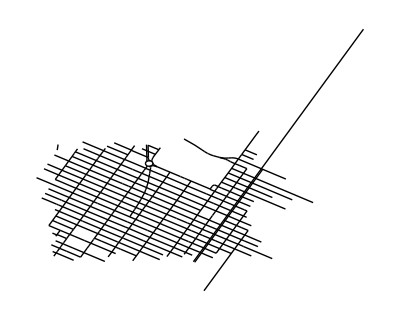

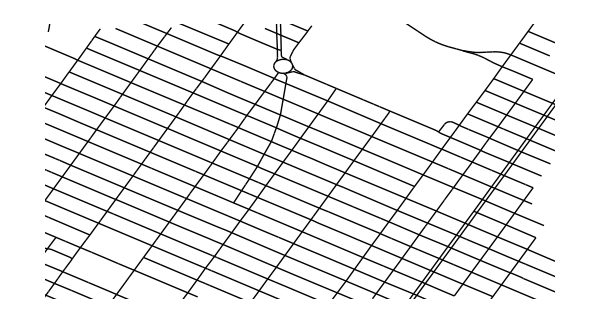

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
GeoGraphics[Values[Line[Values[openStreetMapRegion[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapRegion["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]];

generateLines[openStreetMapData_]:=Values[Line[Values[openStreetMapData[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapData["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]/.
GeoPosition[{a_,b_}]:>{b,a}

Graphics[generateLines[openStreetMapRegion]]
Graphics[generateLines[openStreetMapRegion]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]


ImagePartition[Graphics[generateLines[openStreetMapRegion]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]
, 75]
```